```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
SetDirectory[NotebookDirectory[]]
```

C:\Users\Peter\Documents\MATLAB\PeterB-analysis\lattice

### Constants

```mathematica
c=3*10^8;
hbar = 1.054*10^-34;
kb = 1.38*10^-23;
mLi = 9.9883*10^-27;
γ=2*Pi*6*10^6;
ω0=(2*Pi)/(671*10^-9)*c;
ω = (2*Pi)/(1064*10^-9)*c;
λ=1064*10^-9;
k=(2*Pi)/λ;
Erec = (hbar^2*k^2)/(2*mLi);
ElattVert = (hbar^2*((Sqrt[2]*k)/2)^2)/(2*mLi);
ElattHorz = (hbar^2*((2*k)/2)^2)/(2*mLi);
```

### Lattice Potential

Consider a lattice with spacing α. The natural momentum scale is k =π/α which is the value at the edge of the Brillouin zone. Therefor the natural energy scale is Ε_r= ((ℏ^2(π/α))^2)/(2m)
The ‘Kai Sun’ lattice has  α = λ/(√2). Which gives Ε_r= ((ℏ^2((√2k)/2))^2)/(2m)=14.66KHz  where k=(2π)/(1064nm).
A 2D lattice formed by two retro-reflected 1D lattices with orthogonal polarization has α=λ/2, which yields  Ε_r= ((ℏ^2((2k)/2))^2)/(2m)=30 KHz  where k=(2π)/(1064nm).

For reference, a couple of comments about the lattice. In the Kai Sun paper, they use the following expression:. For perfect vertical polarization, the following are true: Depth = 16 V_0, 4 V_0=V_1, V_2=-0.5 V_1. The external/gaussian confinement is then ω_r = √(32 V_o)/mw_o^2 and ω_(on-site)= 4 √(V_o k^2)/m. In the vertical direction, the expression is ω = √ (4*16 V_o)/mw_z^2

```mathematica
(*Vertical polarization. i.e. the "Kai Sun Lattice"*)
(*Abuse of notation. I'm using E=sqrt(P) per beam. So the expression for the E field is off by some factor, but the expression for the intensity is correct.*)
RetroAttenuation = 1;
W1inplane = 80*10^-6;
W2inplane = 80*10^-6;
Wxmean = Sqrt[W1inplane*W2inplane];
W3inplane = 80*10^-6;
W4inplane = 80*10^-6;
Wymean = Sqrt[W2inplane*W4inplane];
Wz = 80*10^-6;
P = 0.045;
E1=Sqrt[(2*P)/(π*W1inplane*Wz)];
E2=Sqrt[(2*P)/(π*W2inplane*Wz)];
E3=RetroAttenuation*Sqrt[(2*P)/(π*W3inplane*Wz)];
E4=RetroAttenuation*Sqrt[(2*P)/(π*W4inplane*Wz)];
α1=0;
α2=0;
α3=0;
α4=0;
ϵ1 = {0,Sin[α1],Cos[α1]};
ϵ2 = {Sin[α2],0,Cos[α2]};
ϵ3 = {0,Sin[α3],Cos[α3]};
ϵ4={Sin[α4],0,Cos[α4]};

Efld[x_,y_,z_]:=(ϵ1*E1*Exp[I*k*x]*Exp[-(y^2/W1inplane^2)]+ϵ4*E4*Exp[-I*k*x]*Exp[-(y^2/W4inplane^2)]+ϵ2*E2*Exp[I*k*y]*Exp[-(x^2/W2inplane^2)]+ϵ3*E3*Exp[-I*k*y]*Exp[-(x^2/W3inplane^2)])*Exp[-(z^2/Wz^2)];
Intensity[x_,y_,z_]:=Efld[x,y,z].Conjugate[Efld[x,y,z]];
V[x_,y_,z_]:=-(3*Pi*c^2)/(2*ω0^3)*(γ/(ω0-ω)+γ/(ω0+ω))*Intensity[x,y,z];
LattDepthAtoms=V[0,0,0]; (*In μK*)
LatticePot=DensityPlot[V[x*λ,y*λ,0]/ElattVert,{x,-1,1},{y,-1,1},PlotLegends->Automatic,Mesh->10];
PotCutDiag = Plot[{V[t*λ,-t*λ,0]/ElattVert,V[t*λ,t*λ,0]/ElattVert},{t,-1,1},GridLines->Automatic,Frame->True,PlotLabel->"Cuts along x+y and x-y Directions",FrameLabel->{{"Depth (E_r)",""},{"Position (λ)",""}}];
PotCutAxes = Plot[{V[t*λ,0,0]/ElattVert,V[0,t*λ,0]/ElattVert},{t,-1,1},GridLines->Automatic,Frame->True,PlotLabel->"Cuts along x and y Directions",FrameLabel->{{"Depth (E_r)",""},{"Position (λ)",""}}];
PotExtConfinementX = Plot[{V[t*Wxmean,0,0]/ElattVert,(V[0,0,0]+0.5*mLi*(Sqrt[2*Abs[V[0,0,0]]/(Wxmean^2*mLi)])^2*(t*Wxmean)^2)/ElattVert},{t,-1,1},GridLines->Automatic,Frame->True,PlotLabel->"",FrameLabel->{{"Depth (E_r)",""},{"Position (w_o)","Confinement x-axis"}}];
PotExtConfinementY = Plot[{V[0,t*Wymean,0]/ElattVert,(V[0,0,0]+0.5*mLi*(Sqrt[2*Abs[V[0,0,0]]/(Wymean^2*mLi)])^2*(t*Wymean)^2)/ElattVert},{t,-1,1},GridLines->Automatic,Frame->True,PlotLabel->"",FrameLabel->{{"Depth (E_r)",""},{"Position (w_o)","Confinement y-axis"}}];
PlotExtConfinementZ = Plot[{V[0,0,t*Wz]/ElattVert,(V[0,0,0]+0.5*mLi*(Sqrt[4*Abs[V[0,0,0]]/(Wz^2*mLi)])^2*(t*Wz)^2)/ElattVert},{t,-1,1},GridLines->Automatic,Frame->True,PlotLabel->"",FrameLabel->{{"Depth (E_r)",""},{"Position (w_z)","Confinement z-axis"}}];
GraphicsGrid[{{PlotExtConfinementZ,PotExtConfinementX,PotExtConfinementY},{LatticePot,PotCutDiag,PotCutAxes}},ImageSize->Large,Frame->True]
(*Thinking about this along the cut (x,0). the lattice looks like cos(2kx)+2cos(2kx)+2cos(2kx). So the
form of the lattice is dominated by the beams at 45deg to the axes. However, (to first order) only the
cos(2kx) which comes from the beams along the axis is involved in KD scattering. So maybe these plots
are misleading? 05/02/06...not sure what the point of this comment was...need to think about it...*)

(*Horizontal polarization. Normal, separable lattice.*)
Efld2[x_,y_,z_]:=(E1*Exp[I*k*x]*Exp[-(y^2/W1inplane^2)]+E4*Exp[-I*k*x]*Exp[-(y^2/W4inplane^2)])*Exp[-z^2/Wz^2];
Efld3[x_,y_,z_]:=(E2*Exp[I*k*y]*Exp[-(x^2/W2inplane^2)]+E3*Exp[-I*k*y]*Exp[-(x^2/W3inplane^2)])*Exp[-z^2/Wz^2];
Intensity2[x_,y_,z_]:=Efld2[x,y,z]*Conjugate[Efld2[x,y,z]]+Efld3[x,y,z]*Conjugate[Efld3[x,y,z]];
V2[x_,y_,z_]:=-(3*Pi*c^2)/(2*ω0^3)*(γ/(ω0-ω)+γ/(ω0+ω))*Intensity2[x,y,z];
NormalLatticePot=DensityPlot[V2[x*λ,y*λ,0]/ElattHorz,{x,-1,1},{y,-1,1},PlotLegends->Automatic,Mesh->10];
NormalLatticeCutDiag = Plot[{V2[t*λ,t*λ,0]/ElattHorz,V2[t*λ,-t*λ,0]/ElattHorz},{t,-1,1},GridLines->Automatic,Frame->True,PlotLabel->"Cuts along x+y and x-y Directions",FrameLabel->{{"Depth (E_r)",""},{"Position (λ)",""}}];
NormalLatticeCutAxes =Plot[{V2[t*λ,0,0]/ElattHorz,V2[0,t*λ,0]/ElattHorz},{t,-1,1},GridLines->Automatic,Frame->True,PlotLabel->"Cuts along x and y Directions",FrameLabel->{{"Depth (E_r)",""},{"Position (λ)",""}}];
NormalExtConfinementX = Plot[{V2[t*Wxmean,0,0]/ElattHorz,(V2[0,0,0]+0.5*mLi*(Sqrt[Abs[2*V2[0,0,0]]/(Wxmean^2*mLi)])^2*(t*Wxmean)^2)/ElattHorz},{t,-1,1},GridLines->Automatic,Frame->True,PlotLabel->"",FrameLabel->{{"Depth (E_r)",""},{"Position (w_o)","Confinement x-axis"}}];
NormalExtConfinementY = Plot[{V2[0,t*Wymean,0]/ElattHorz,(V2[0,0,0]+0.5*mLi*(Sqrt[Abs[2*V2[0,0,0]]/(Wymean^2*mLi)])^2*(t*Wymean)^2)/ElattHorz},{t,-1,1},GridLines->Automatic,Frame->True,PlotLabel->"",FrameLabel->{{"Depth (E_r)",""},{"Position (w_o)","Confinement y-axis"}}];
NormalExtConfinementZ = Plot[{V2[0,0,t*Wz]/ElattHorz,(V2[0,0,0]+0.5*mLi*(Sqrt[Abs[4*V2[0,0,0]]/(Wz^2*mLi)])^2*(t*Wz)^2)/ElattHorz},{t,-1,1},GridLines->Automatic,Frame->True,PlotLabel->"",FrameLabel->{{"Depth (E_r)",""},{"Position (w_o)","Confinement z-axis"}}];
GraphicsGrid[{{NormalExtConfinementZ,NormalExtConfinementX,NormalExtConfinementY},{NormalLatticePot,NormalLatticeCutDiag,NormalLatticeCutAxes}},ImageSize->Large,Frame->True]

(*Summary table. Note that you must be careful with the 'depth' for the Horizontal lattice, since the quoted depth is relative to infinity, and it is not the same as the hopping barrier. Note also that the relevant depth for the Horizontal lattice is typically the individual depth of the the lattices in each direction...not their combined depth. So, for example, it is not V2[0,0] but V2[0,0]/2 that enters in the calculation of trap frequencies.*)
Grid[Transpose[{{"","Depth (μK)","Depth (E_latt)","E_latt (kHz)","Ext-x Confinement (Hz)","Ext-y Confinement (Hz)","Ext-z Confinement (Hz)","On-Site Confinement (KHz)"},{"Vert Polarization",Abs[V[0,0,0]]/(kb)/10^-6,Abs[V[0,0,0]]/ElattVert,ElattVert/(2*π*hbar)/10^3,Sqrt[2*Abs[V[0,0,0]]/(Wxmean^2*mLi)]/(2*π),Sqrt[2*Abs[V[0,0,0]]/(Wymean^2*mLi)]/(2*π),Sqrt[Abs[4*V[0,0,0]]/(Wz^2*mLi)]/(2*π),Sqrt[Abs[V[0,0,0]]*k^2/mLi]/(2*π)/10^3},{"Horz Polarization",Abs[V2[0,0,0]]/(kb)/10^-6,Abs[V2[0,0,0]]/ElattHorz,ElattHorz/(2*π*hbar)/10^3,Sqrt[Abs[2*V2[0,0,0]]/(Wxmean^2*mLi)]/(2*π),Sqrt[Abs[2*V2[0,0,0]]/(Wymean^2*mLi)]/(2*π),Sqrt[Abs[4*V2[0,0,0]]/(Wz^2*mLi)]/(2*π),4*Sqrt[Abs[V2[0,0,0]/2]*k^2/mLi]/(2*π)/10^3}}],Frame->All]
```

-Graphics-

-Graphics-

| Vert Polarization | Horz Polarization
Depth (μK) | 4.42461 | 2.21231
Depth (E_latt) | 6.29721 | 1.5743
E_latt (kHz) | 14.6415 | 29.283
Ext-x Confinement (Hz) | 219.977 | 155.547
Ext-y Confinement (Hz) | 219.977 | 155.547
Ext-z Confinement (Hz) | 311.094 | 219.977
On-Site Confinement (KHz) | 73.4835 | 146.967

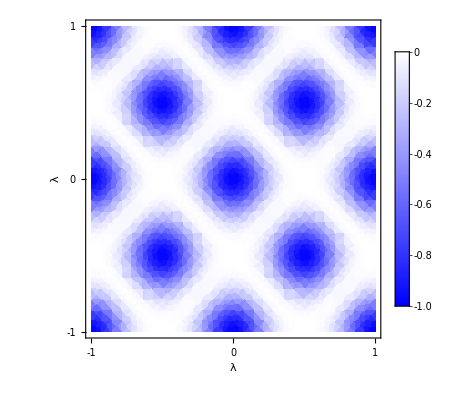

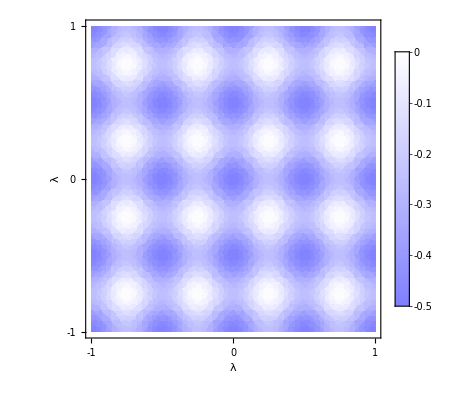

```mathematica
LatticePot=DensityPlot[V[x*λ,y*λ,0]/Abs[V[0,0,0]],{x,-1,1},{y,-1,1},ColorFunction->(RGBColor[#,#,1]&),FrameLabel->{"λ","λ"},PlotLegends->Automatic,LabelStyle->Directive[Black,12],FrameTicks->{{{-1,0,1},None},{{-1,0,1},None}}]
NormalLatticePot=DensityPlot[V2[x*λ,y*λ,0]/Abs[V[0,0,0]],{x,-1,1},{y,-1,1},ColorFunction->(RGBColor[#*.5+0.5,#*0.5+0.5,1]&),PlotLegends->Automatic,PlotRange->{Automatic,Automatic,{-1,0}},FrameLabel->{"λ","λ"},LabelStyle->Directive[Black,12],FrameTicks->{{{-1,0,1},None},{{-1,0,1},None}}]
Export["4FoldLattice.pdf",LatticePot];
Export["NormalLattice.pdf",NormalLatticePot];
```

### Kapitza-Dirac

Exp[cos(2kx)+cos(2ky)+2cos(2kx+2ky)+2cos(2kx-2ky)]=Exp[cos(kx)]*Exp[cos(ky)]*Exp[2cos(kx+ky)]*Exp[2cos(kx-ky)]
So up to first order processes, each of these behaves like an independent lattice...for purposes of KD scattering.
=[Σ_n J_n()Exp(2knx)]*[Σ_m J_m()Exp(2kmy)]*[Σ_q J_q()Exp(2kq(x-y))]*[Σ_l J_l()Exp(2kl(x-y))]
For second order terms, notice that 45deg directions can scatter into the same momentum states as the first order from the 0deg.
However, the opposite is not possible. The second order terms for the 0deg lattice could only scatter into the 2√2k states.

| ω | f | Beams
ωrpxmx | 591325. | 94112.3 | 1&4
ωrpymy | 591325. | 94112.3 | 2&3
ωrpymx | 1.18265×10^6 | 188225. | 1&2, 3&4
ωrpypx | 1.18265×10^6 | 188225. | 1&3, 2&4

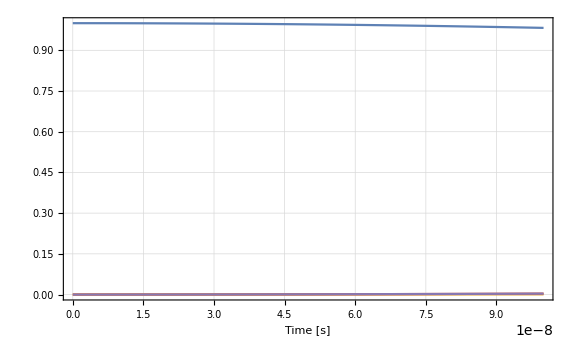

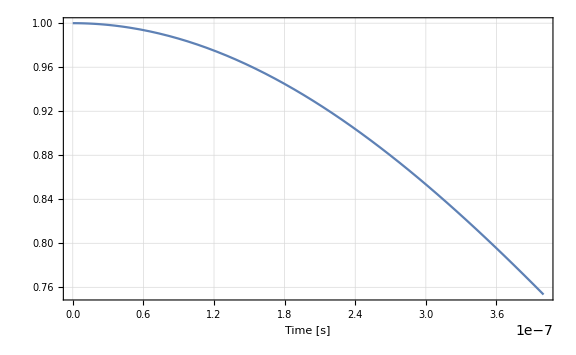

```mathematica
ωrpxmx=1/hbar*(2*(3*Pi*c^2)/(2*ω0^3)*(γ/(ω0-ω)+γ/(ω0+ω)))*2*E1*E4 ;(* i.e. formed by positive moving x beam and negative moving x beam. Final *2 due to lithium molecules*)
ωrpymy=1/hbar*(2*(3*Pi*c^2)/(2*ω0^3)*(γ/(ω0-ω)+γ/(ω0+ω)))*2*E2*E3;
ωrpymx=1/hbar*(2*(3*Pi*c^2)/(2*ω0^3)*(γ/(ω0-ω)+γ/(ω0+ω)))*2*(E1*E2+E3*E4) ;(* same as ωrmypx*)
ωrpypx=1/hbar*(2*(3*Pi*c^2)/(2*ω0^3)*(γ/(ω0-ω)+γ/(ω0+ω)))*2*(E1*E3+E2*E4);(* same as ωrmymx*)
Grid[Transpose[{{"","ωrpxmx","ωrpymy","ωrpymx","ωrpypx"},{"ω",ωrpxmx,ωrpymy,ωrpymx,ωrpypx},{"f",ωrpxmx/(2*Pi),ωrpymy/(2*Pi),ωrpymx/(2*Pi),ωrpypx/(2*Pi)},{"Beams","1&4","2&3","1&2, 3&4","1&3, 2&4"}}],Frame->All]
KzeroPop[t_]:= (BesselJ[0,ωrpxmx*t]*BesselJ[0,ωrpymy*t]*BesselJ[0,ωrpymx*t]*BesselJ[0,ωrpymx*t])^2;
KonePop[t_]:=(BesselJ[1,ωrpxmx*t]*BesselJ[0,ωrpymy*t]*BesselJ[0,ωrpymx*t]*BesselJ[0,ωrpymx*t])^2;
Kone2Pop[t_]:=Overscript[(BesselJ[0,ωrpxmx*t]*BesselJ[1,ωrpymy*t]*BesselJ[0,ωrpymx*t]*BesselJ[0,ωrpymx*t])^2, 2];
Kone3Pop[t_]:=(BesselJ[0,ωrpxmx*t]*BesselJ[0,ωrpymy*t]*BesselJ[1,ωrpymx*t]*BesselJ[0,ωrpymx*t])^2;
Kone4Pop[t_]:=(BesselJ[0,ωrpxmx*t]*BesselJ[0,ωrpymy*t]*BesselJ[0,ωrpymx*t]*BesselJ[1,ωrpymx*t])^2;
Plot[{KzeroPop[t],KonePop[t],Kone2Pop[t],Kone3Pop[t],Kone4Pop[t]},{t,0,0.1*10^-6},ImageSize->Large,GridLines->Automatic,Frame->True,AxesLabel->{"Time [s]"}]
Plot[KzeroPop[t],{t,0,0.4*10^-6},ImageSize->Large,GridLines->Automatic,Frame->True,AxesLabel->{"Time [s]"}]
```